```mathematica
(* Compute intersection "times" between two lines moving at unit speed, presented as point, angle *)

computeintersection[p1_,th1_,p3_,th3_]:=Module[{u1,u2,p2=p1+{Cos[th1],Sin[th1]},p4=p3+{Cos[th3],Sin[th3]},pos},
u1=((p4[[1]]-p3[[1]])(p1[[2]]-p3[[2]])-(p4[[2]]-p3[[2]])(p1[[1]]-p3[[1]]))/((p4[[2]]-p3[[2]])(p2[[1]]-p1[[1]])-(p4[[1]]-p3[[1]])(p2[[2]]-p1[[2]]));
u2=((p2[[1]]-p1[[1]])(p1[[2]]-p3[[2]])-(p2[[2]]-p1[[2]])(p1[[1]]-p3[[1]]))/((p4[[2]]-p3[[2]])(p2[[1]]-p1[[1]])-(p4[[1]]-p3[[1]])(p2[[2]]-p1[[2]]));
(*pos=p1+u1{Cos[th1],Sin[th1]};*)
{u1,u2(*,pos*)}
]

getallintersections[list_]:=Module[{numlines=Length[list],temp,inter},
temp=Reap[
Do[
If[i<j,
inter=computeintersection[list[[i,1]],list[[i,2]],list[[j,1]],list[[j,2]]];
Sow[{{i,j},(* both lines stop at the max time, but we need both times *)
inter[[1;;2]]}]
],
{i,numlines-1},{j,numlines}];];
temp[[2,1]]
]

(* plotting functions *)
plotlines[list_]:=Graphics[Table[Line[{list[[i,1]],list[[i,1]]+{Cos[list[[i,2]]],Sin[list[[i,2]]]}}],{i,Length[list]}]]
(* with arrows (too messy)*)
plotlinesa[list_,ends_,cutoff_]:=Graphics[Table[{Point[list[[i,1]]],Arrow[{list[[i,1]],list[[i,1]]+Min[ends[[i]],cutoff]{Cos[list[[i,2]]],Sin[list[[i,2]]]}}]},{i,Length[list]}]]
(* lines*)
plotlines2[list_,ends_,cutoff_]:=Graphics[Table[{Point[list[[i,1]]],Line[{list[[i,1]],list[[i,1]]+Min[ends[[i]],cutoff]{Cos[list[[i,2]]],Sin[list[[i,2]]]}}]},{i,Length[list]}]]

(* make the set of rays by putting down grid points and choosing random angles *)
makegrid[m_,n_]:=Table[{{i,j},RandomReal[{0,2π}]},{i,0,m-1},{j,0,n-1}]

(* compute end times and connected components from a set of rays *)
Truncate[linelist_]:=Module[{living,numlines=Length[linelist],ends,time,postime,postimemax,sortedtime,entry,t1,t2,ind=0,components,p1,p2,c1,c2,temp},
living=Table[i,{i,numlines}];
ends=Table[Infinity,{numlines}];
time=getallintersections[linelist];
postime=Select[time,((#[[2,1]]>0)&&(#[[2,2]]>0))&];
postimemax=Table[{postime[[i,1]],Max[postime[[i,2]]]},{i,Length[postime]}];
sortedtime=Sort[postimemax,#1[[2]]<#2[[2]]&];
(*Print[time,postime,postimemax,sortedtime];*)
living=Select[living,Not[MemberQ[sortedtime[[1,1]],#]]&];
components={sortedtime[[1,1]]};
ends[[sortedtime[[1,1]]]]=sortedtime[[1,2]];
sortedtime=Drop[sortedtime,1];
(*Print[living];*)
While[(* could also check if list of intersections is used up?, that would be an error, most likely*)
((Length[living]>0)&&(ind<numlines^2)),
(*need to check whether next pair in sorted list has been preempted or not by seeing if it's less than "ends"*)
While[(* two lines intersect at most once, so we pull up the entry for the intersection using the pair to get the coordinates along the two lines *)
If[Length[sortedtime]>0,entry=Select[postime,#[[1]]==sortedtime[[1,1]]&][[1]];
(*Print[ends[[sortedtime[[1,1]]]]];
Print[entry];*)
(* if either coordinate is greater than the "end", then this intersection was preempted *)
(entry[[2,1]]>ends[[sortedtime[[1,1,1]]]])||(entry[[2,2]]>ends[[sortedtime[[1,1,2]]]]),False],
sortedtime=Drop[sortedtime,1]];
If[Length[sortedtime]==0,Break[]];
(*Print[sortedtime[[1,1]]];*)
living=Select[living,Not[MemberQ[sortedtime[[1,1]],#]]&];
p1=Position[components,sortedtime[[1,1,1]]];
p2=Position[components,sortedtime[[1,1,2]]];
c1=If[Length[p1]>0,temp=components[[p1[[1,1]]]];
components=Select[components,Not[MemberQ[#,sortedtime[[1,1,1]]]]&];
temp,{sortedtime[[1,1,1]]}];
c2=If[Length[p2]>0,temp=components[[p2[[1,1]]]];
components=Select[components,Not[MemberQ[#,sortedtime[[1,1,2]]]]&];
temp,{sortedtime[[1,1,2]]}];
temp=Union[c1,c2];
components=Append[components,temp];
(* only want to replace Infinities, not other times *)
t1=ends[[sortedtime[[1,1]]]];
t2=Table[If[t1[[i]]<Infinity,
Min[t1[[i]],sortedtime[[1,2]]],
sortedtime[[1,2]]],{i,2}];
ends[[sortedtime[[1,1]]]]=t2;
sortedtime=Drop[sortedtime,1];
(*Print[living];*)
ind++;
];
{ends,components}
]
```

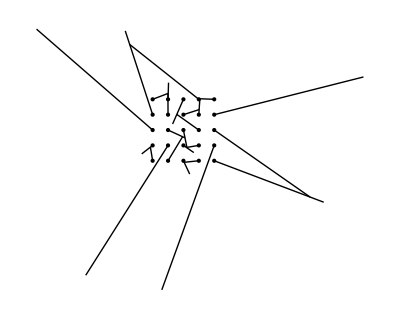

```mathematica
test=Flatten[makegrid[5,5],1];
{ends,components}=Truncate[test];
plotlines2[test,ends,10]
```

```mathematica
test=Flatten[makegrid[15,15],1];
{ends,components}=Truncate[test];
```

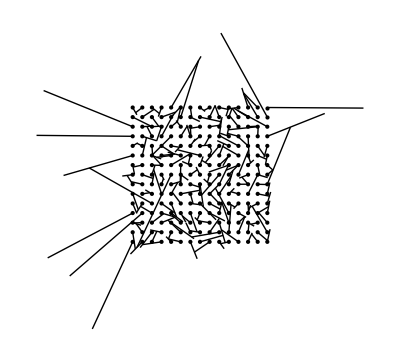

```mathematica
plotlines2[test,ends,10]
```

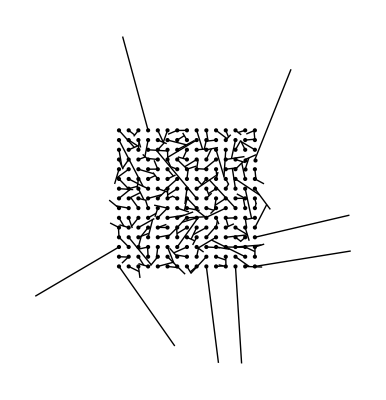

```mathematica
timestest=Table[test=Flatten[makegrid[n,n],1];
Timing[{ends,components}=Truncate[test];][[1]],{n,3,15}];
plotlines2[test,ends,10]
```

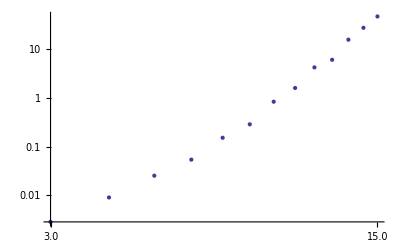

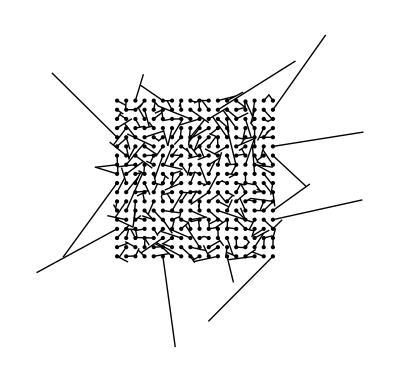

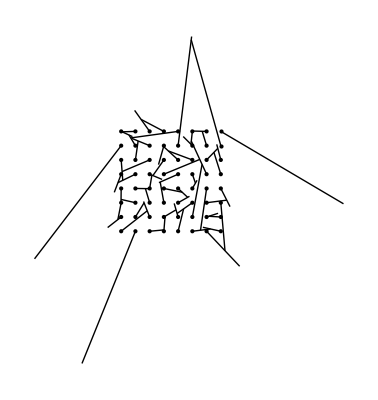

```mathematica
timestest2=Table[{i,timestest[[i-2]]},{i,3,15}];
ListLogLogPlot[timestest2,PlotStyle->PointSize[Large]]
```

{{130,131},{11,26},{52,53},{120,135},{218,219},{21,36},{156,171},{127,128},{15,30},{71,86},{101,117},{98,113},{99,100},{182,183,198},{150,165},{9,24},{172,187,188},{205,220},{103,118},{181,196},{193,207},{95,96},{104,105},{3,17,18},{79,93},{116,132},{23,37},{43,44},{108,109,123},{7,8,22},{31,47},{202,216},{144,160},{206,221},{201,215},{87,102},{61,62,76},{134,149},{197,211},{199,213,214},{55,56,85},{29,45,60},{73,88,90},{50,64,65},{66,67,80,82,83,84},{5,6,20,34},{167,168,169},{122,124},{33,48,49,77,78},{145,161,175},{91,121},{25,27,58},{81,97,111},{32,46},{92,94,107},{14,28,42},{142,159},{186,203,204},{125,139,153},{114,129,146},{119,133,147,148,176},{141,157,158,174},{69,115},{106,136,138,151,166},{57,59,74},{38,39,51},{40,41,54,70,72},{173,189,190,192},{110,112,143},{195,209,210},{152,155,170},{63,137},{126,140,154},{162,163,177,191,208},{184,185,200,212},{164,178,179,180,194,223},{75,89},{217,222},{10,35},{2,16,68}}

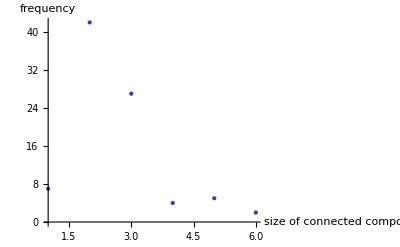

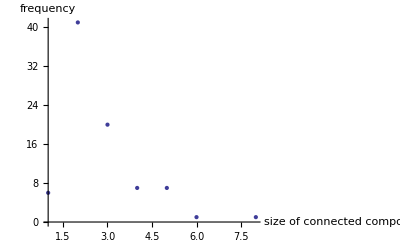

```mathematica
components
clist=Table[Length[components[[i]]],{i,Length[components]}];
tlist=Join[{{1,Count[ends,Infinity]}},Tally[clist]];
ListPlot[tlist,PlotStyle->PointSize[Large],AxesLabel->{"size of connected component","frequency"}]
```

{∞,1.7709,0.9114,∞,1.13138,1.75572,1.0913,1.0913,0.981756,7.48494,0.615076,∞,∞,2.12502,0.875925,1.7709,1.08674,0.9114,∞,1.13138,0.807533,1.20216,1.18616,0.981756,1.91421,0.615076,1.56396,1.15246,1.47636,0.875925,1.21377,2.01308,1.53765,1.37955,7.48494,0.807533,1.18616,1.04084,1.04084,1.03113,1.03113,1.15246,1.18929,1.18929,1.00148,2.01308,1.21377,1.48427,1.36624,1.72345,2.67923,0.620987,0.620987,1.31047,1.40124,1.47568,2.53424,1.56396,1.57599,1.00148,0.760683,0.760683,2.90731,1.5323,1.5323,1.38482,1.05566,8.35006,2.40975,1.49567,0.878692,2.7208,0.80199,1.57599,6.17089,1.31782,1.84095,1.36624,1.09408,1.48344,2.0062,0.969483,0.969483,1.72346,1.40124,0.878692,1.25017,0.80199,6.17089,1.56068,1.90235,1.0875,1.09408,2.07316,1.07359,1.07359,0.988372,0.896188,0.930264,0.930264,0.892402,1.25017,1.00481,1.08152,1.08152,2.4882,1.0875,0.768092,0.768092,2.38603,0.988372,2.38603,0.896188,0.958665,2.40975,1.09998,0.892402,1.00481,2.21219,0.672649,1.90235,1.79215,1.20064,1.79215,1.24458,1.41483,0.828572,0.828572,0.958665,0.544686,0.544686,1.09998,1.05808,1.31847,0.672649,0.882681,2.90731,2.17608,1.24458,1.41483,2.28577,2.20855,2.80353,1.23626,1.32544,2.25567,1.80755,1.05808,1.31847,0.956112,0.882681,2.87763,2.2486,2.95493,0.74534,0.814161,1.49728,1.38639,2.20855,1.23626,1.32544,0.952213,0.952213,0.973227,0.956112,2.18088,1.76024,0.914141,0.914141,0.74534,0.814161,0.991388,2.79709,1.38639,1.88492,2.25784,1.17849,1.4949,1.12641,0.973227,1.03022,0.949062,0.72795,0.868932,0.868932,2.23774,0.989572,0.989572,0.806136,0.806136,1.51667,2.31369,1.06129,1.75316,2.14317,1.03022,1.34985,0.72795,1.31456,0.91124,1.24622,1.21866,1.08648,1.08648,1.00026,1.23651,1.06129,3.08055,2.83648,2.14317,1.34985,3.14015,1.39153,1.31456,1.24622,1.21866,6.43001,0.766818,0.766818,1.00026,1.23651,6.43001,3.48083,∞,∞}

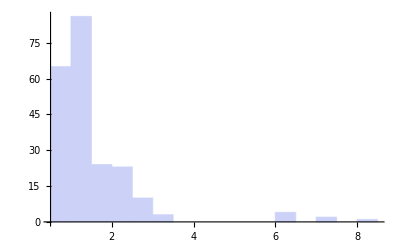

8.35006

7

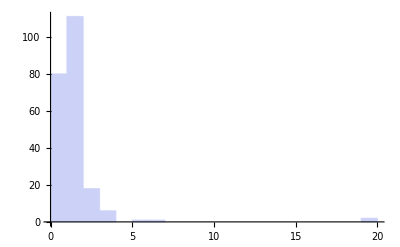

19.0737

6

```mathematica
ends
Histogram[Select[ends,#<20&]]
Max[Select[ends,#≠Infinity&]]
Count[ends,Infinity]
```

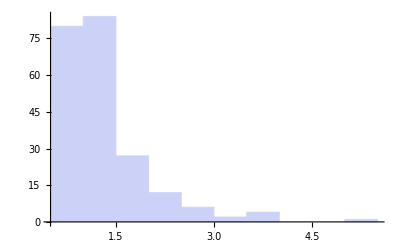

```mathematica
Histogram[Select[ends,#<6&]]
```

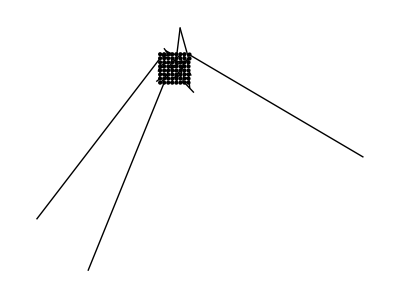

```mathematica
plotlines2[test,ends,50]
```